# 2. domača naloga

## 1. naloga

a)  Definirajte funkcijo , ki sprejme naravni števili  in  in vrne matriko dimenzije , kjer se na vsakem mestu v matriki pojavi vsota indeksa stolpca in indeksa vrstice.
b) Izračunajte lastne vrednosti in lastne vektorje matrike .
c)  Narišite lastne vektorje matrike .
d) Izračunajte karakteristični polinom matrike .
e) Matriko  diagonalizirajte. Določite ustrezno diagonalno matriko , prehodno matriko  in .
f) Rešite matrično enačbo .

```mathematica
A[n_, m_]:= Table[i+j, {i, 1, n}, {j, 1, m}]
```

```mathematica
mat = A[3, 3]
```

{{2,3,4},{3,4,5},{4,5,6}}

```mathematica
{eigenvalue, eigenvectors} = Eigensystem[mat]
```

{{6+√42,6-√42,0},{{-(-17-2 √42)/(23+4 √42),-(-20-3 √42)/(23+4 √42),1},{-(17-2 √42)/(-23+4 √42),-(20-3 √42)/(-23+4 √42),1},{1,-2,1}}}

```mathematica
Graphics3D[
{
Red, Arrow[{ {0, 0, 0}, eigenvectors[[1]]}],
Green, Arrow[{ { 0, 0, 0}, eigenvectors[[2]]}],
Blue, Arrow[{ { 0, 0, 0}, eigenvectors[[3]]}]
},
Axes -> True,
PlotRange->All,
Boxed->True
]
```

-Graphics3D-

```mathematica
polynom = CharacteristicPolynomial[mat, λ]
```

6 λ+12 λ^2-λ^3

```mathematica
G= DiagonalMatrix[eigenvalue]
```

{{6+√42,0,0},{0,6-√42,0},{0,0,0}}

```mathematica
P = Transpose[eigenvectors]
```

{{-(-17-2 √42)/(23+4 √42),-(17-2 √42)/(-23+4 √42),1},{-(-20-3 √42)/(23+4 √42),-(20-3 √42)/(-23+4 √42),-2},{1,1,1}}

```mathematica
Simplify[P . G . Inverse[P] - mat]
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
inverzP = Inverse[P]
```

{{(2-20/(-23+4 √42)+(3 √42)/(-23+4 √42))/(54/(-23+4 √42)-(7 √42)/(-23+4 √42)+54/(23+4 √42)+(7 √42)/(23+4 √42)+(22 √42)/((-23+4 √42) (23+4 √42))),(1+17/(-23+4 √42)-(2 √42)/(-23+4 √42))/(54/(-23+4 √42)-(7 √42)/(-23+4 √42)+54/(23+4 √42)+(7 √42)/(23+4 √42)+(22 √42)/((-23+4 √42) (23+4 √42))),(54/(-23+4 √42)-(7 √42)/(-23+4 √42))/(54/(-23+4 √42)-(7 √42)/(-23+4 √42)+54/(23+4 √42)+(7 √42)/(23+4 √42)+(22 √42)/((-23+4 √42) (23+4 √42)))},{(-2-20/(23+4 √42)-(3 √42)/(23+4 √42))/(54/(-23+4 √42)-(7 √42)/(-23+4 √42)+54/(23+4 √42)+(7 √42)/(23+4 √42)+(22 √42)/((-23+4 √42) (23+4 √42))),(-1+17/(23+4 √42)+(2 √42)/(23+4 √42))/(54/(-23+4 √42)-(7 √42)/(-23+4 √42)+54/(23+4 √42)+(7 √42)/(23+4 √42)+(22 √42)/((-23+4 √42) (23+4 √42))),(54/(23+4 √42)+(7 √42)/(23+4 √42))/(54/(-23+4 √42)-(7 √42)/(-23+4 √42)+54/(23+4 √42)+(7 √42)/(23+4 √42)+(22 √42)/((-23+4 √42) (23+4 √42)))},{(20/(-23+4 √42)-(3 √42)/(-23+4 √42)+20/(23+4 √42)+(3 √42)/(23+4 √42))/(54/(-23+4 √42)-(7 √42)/(-23+4 √42)+54/(23+4 √42)+(7 √42)/(23+4 √42)+(22 √42)/((-23+4 √42) (23+4 √42))),(-17/(-23+4 √42)+(2 √42)/(-23+4 √42)-17/(23+4 √42)-(2 √42)/(23+4 √42))/(54/(-23+4 √42)-(7 √42)/(-23+4 √42)+54/(23+4 √42)+(7 √42)/(23+4 √42)+(22 √42)/((-23+4 √42) (23+4 √42))),(22 √42)/((-23+4 √42) (23+4 √42) (54/(-23+4 √42)-(7 √42)/(-23+4 √42)+54/(23+4 √42)+(7 √42)/(23+4 √42)+(22 √42)/((-23+4 √42) (23+4 √42))))}}

```mathematica
I = IdentityMatrix[3]
```

Set::wrsym: Symbol ⅈ is Protected.

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
M = mat + P - G
```

{{-4-√42-(-17-2 √42)/(23+4 √42),3-(17-2 √42)/(-23+4 √42),5},{3-(-20-3 √42)/(23+4 √42),-2+√42-(20-3 √42)/(-23+4 √42),3},{5,6,7}}

```mathematica
X = Inverse[M].I
```

{{(-32+7 √42-140/(-23+4 √42)+(21 √42)/(-23+4 √42))/(-44-21 √42+280/(-23+4 √42)-(31 √42)/(-23+4 √42)+224/(23+4 √42)+(82 √42)/(23+4 √42)+(154 √42)/((-23+4 √42) (23+4 √42))),(9+119/(-23+4 √42)-(14 √42)/(-23+4 √42))/(-44-21 √42+280/(-23+4 √42)-(31 √42)/(-23+4 √42)+224/(23+4 √42)+(82 √42)/(23+4 √42)+(154 √42)/((-23+4 √42) (23+4 √42))),(19-5 √42+49/(-23+4 √42)-(9 √42)/(-23+4 √42))/(-44-21 √42+280/(-23+4 √42)-(31 √42)/(-23+4 √42)+224/(23+4 √42)+(82 √42)/(23+4 √42)+(154 √42)/((-23+4 √42) (23+4 √42)))},{(-6-140/(23+4 √42)-(21 √42)/(23+4 √42))/(-44-21 √42+280/(-23+4 √42)-(31 √42)/(-23+4 √42)+224/(23+4 √42)+(82 √42)/(23+4 √42)+(154 √42)/((-23+4 √42) (23+4 √42))),(-53-7 √42+119/(23+4 √42)+(14 √42)/(23+4 √42))/(-44-21 √42+280/(-23+4 √42)-(31 √42)/(-23+4 √42)+224/(23+4 √42)+(82 √42)/(23+4 √42)+(154 √42)/((-23+4 √42) (23+4 √42))),(27+3 √42+49/(23+4 √42)+(9 √42)/(23+4 √42))/(-44-21 √42+280/(-23+4 √42)-(31 √42)/(-23+4 √42)+224/(23+4 √42)+(82 √42)/(23+4 √42)+(154 √42)/((-23+4 √42) (23+4 √42)))},{(28-5 √42+100/(-23+4 √42)-(15 √42)/(-23+4 √42)+120/(23+4 √42)+(18 √42)/(23+4 √42))/(-44-21 √42+280/(-23+4 √42)-(31 √42)/(-23+4 √42)+224/(23+4 √42)+(82 √42)/(23+4 √42)+(154 √42)/((-23+4 √42) (23+4 √42))),(39+6 √42-85/(-23+4 √42)+(10 √42)/(-23+4 √42)-102/(23+4 √42)-(12 √42)/(23+4 √42))/(-44-21 √42+280/(-23+4 √42)-(31 √42)/(-23+4 √42)+224/(23+4 √42)+(82 √42)/(23+4 √42)+(154 √42)/((-23+4 √42) (23+4 √42))),(-43-2 √42+5/(-23+4 √42)+(2 √42)/(-23+4 √42)-10/(23+4 √42)+(4 √42)/(23+4 √42)+(22 √42)/((-23+4 √42) (23+4 √42)))/(-44-21 √42+280/(-23+4 √42)-(31 √42)/(-23+4 √42)+224/(23+4 √42)+(82 √42)/(23+4 √42)+(154 √42)/((-23+4 √42) (23+4 √42)))}}.ⅈ

## 2. naloga

Imamo klančino z naklonom 30 stopinj dolžine 10m. Na dnu klančine se nahaja ravnina dolžine 10m. Na levem in desnem robu se nahaja stena (glej sliko). 
Kroglico z radijem 10cm spustimo na vrhu klanca, da se začne gibati pod vplivom gravitacije. Predpostavite lahko, da med kroglico in podlago ni trenja in 
da se zaradi kotaljenja energija ne izgublja. Ko pride kroglica na dno klanca, se giblje v vodoravni smeri z enako velikim vektorjem hitrosti (predpostavi, 
da je kot dovolj majhen, da na pride do odboja). 
Simulirajte kotaljenje kroglice po klančini in ravnini, ki se odbija od desnega roba.
Za gravitacijski pospešek vzemite g = 9.81, začetna hitrost kroglice naj bo v0 = 0.

a) Definiraj gravitacijski pospešek, naklon, dolžino klanca, začetno hitrost in radij kroglice.

```mathematica
g = 9.81;
```

```mathematica
l = 10;
```

```mathematica
v0 = 0;
```

```mathematica
r = 0.1;
```

```mathematica
fi = 30 Degree;
```

```mathematica
h = l Sin[fi];
```

```mathematica
dolzina = l Cos[fi];
```

```mathematica
visinaSten = 3;
```

b) Nariši klančino, tla in obe steni.

```mathematica
tla = Line[{{0, 0}, {l+dolzina, 0}}];
```

```mathematica
klancina = Line[{{0, h}, {dolzina, 0}}];
```

```mathematica
leviZid = Line[{{0, 0},{0, h+visinaSten}}];
```

```mathematica
desniZid = Line[{{l+dolzina, 0}, {l+dolzina, visinaSten}}];
```

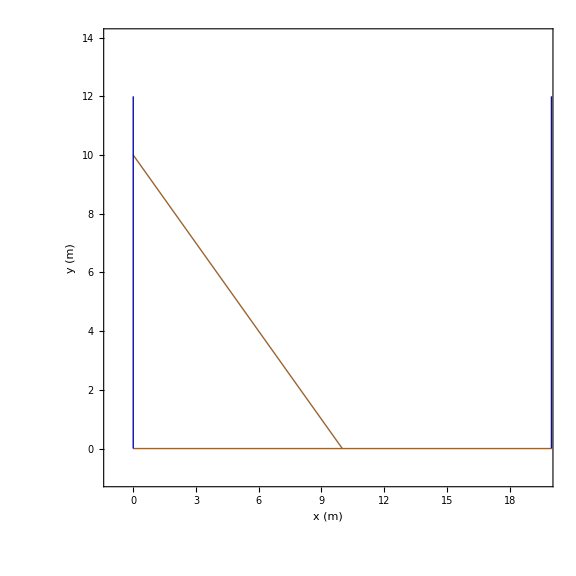

```mathematica
slika = Graphics[{Thick,Brown,tla,klancina,Blue,leviZid,desniZid},Axes->True,AxesOrigin->{0,0},PlotRange->{{-1,l+1+dolzina},{-1,h+visinaSten+1}},AspectRatio->1,Frame->True,FrameLabel->{"x (m)","y (m)"},ImageSize->Large]
```

c) Na sliko dodaj kroglico tako, da se bo kroglica premaknila, če se spremeni njeno središče.

```mathematica
Manipulate[
Show[
slika,
Graphics[{Red, Disk[{x, y}, 0.1]}]
],
{{x, 0}, "x center", 0, 10},
{{y, h}, "y center", 0, 6}
]
```

d) Definiraj funkcijo `naKlancu`, ki sprejme središče kroglice in vrne `True`, če je kroglica na klancu.

```mathematica
toleranca= 0.1;
```

```mathematica
naKlancu[{x_, y_}]:=Module[{yKlanec}, If[0<= x <= dolzina, yKlanec=h - (h/dolzina)x; Abs[y-yKlanec] <= toleranca, False]]
```

```mathematica
naKlancu[{0, h}]
```

True

```mathematica
naKlancu[{5, 1}]
```

False

e) Definiraj funkcijo `desniRob`, ki sprejme središče kroglice in vrne `True`, če je kroglica trčila ob desni rob.

```mathematica
desniRob[{x_, y_}]:=x+r>=l
```

```mathematica
desniRob[{10-5,0}]
```

False

f) Definiraj funkcijo `posodobiHitrost`, ki sprejme vektor trenutne hitrost kroglice in kot α ter vrne novo hitrost, gibanja po klančini z naklonom α.

```mathematica
posodobiHitrost[v_?VectorQ, alpha_, dt_: 0.01]:= Module[
{
a = g*Sin[alpha],
smer = {Cos[alpha], -Sin[alpha]},
vNovo
},
vNovo = v + a*dt*smer;
vNovo
]
```

```mathematica
posodobiHitrost[{0, 0}, fi]
```

{0.0424785,-0.024525}

g) Definiraj funkcijo `hitrostNaKlanec`, ki sprejme vektor trenutne hitrosti kroglice in kot α ter vrne novo hitrost, ki jo dobi kroglica, ko iz ravnega dela preide na klanec z naklonom α.

```mathematica
hitrostNaKlanec[v_?VectorQ, alpha_]:=Module[
{
t = {Cos[alpha], -Sin[alpha]},
vProj
},
vProj = (v.t) t;
vProj
]
```

```mathematica
hitrostNaKlanec[{0, 0}, fi]
```

{0,0}

h) Definiraj funkcijo `hitrostSKlanca`, ki sprejme vektor trenutne hitrosti kroglice in vrne novo hitrost, ki jo dobi kroglica, ko s klanca preide na ravni del.

```mathematica
hitrostSKlanca[v_?VectorQ]:={Norm[v], 0}
```

i) S pomočjo prejšnjih funkcij simuliraj premikanje kroglice.